```mathematica
SetDirectory[NotebookDirectory[]];
test  =Flatten[Import["yeon-data/A0.json"],1]
```

{T→0,gamma→0.053,t50→1.5,Cexp→{100,100,100,94.2,85.4,84.7,83.2,81.,78.8,77.4,76.6,76.6,76.6}}

```mathematica
dataA0 = "Cexp"/.test
```

{100,100,100,94.2,85.4,84.7,83.2,81.,78.8,77.4,76.6,76.6,76.6}

{t→-0.261471,γ→-0.0618787,β→2.68472,μ→-0.917566}

100 ⅇ^(0.033286 (1-ⅇ^(-2.68472 x)-2.68472 x)+0.0618787 x)

{{0.,100.},{0.5,101.091},{1.,100.354},{1.5,99.1501},{2.,97.8398},{2.5,96.5154},{3.,95.201},{3.5,93.9024},{4.,92.6209},{4.5,91.3568},{5.,90.11},{5.5,88.8801},{6.,87.667}}

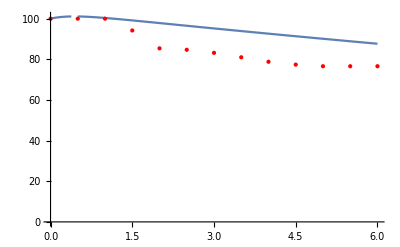

0.480321

```mathematica
FindFit[dataA0,dataA0⟦1⟧ Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{t , γ,β,μ},x, Method->NMinimize]
fit0 = dataA0⟦1⟧Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/.%
Table[{i,(%/.{x-> i})},{i,0,6,0.5}]
Show[Plot[%%,{x,0,6}, PlotRange->{Min[data,%],Max[data,%]}],Graphics[{Red, Point[{Table[i,{i,0,6,0.5}],dataA0}ᵀ]}]]
Norm[Abs[dataA0- %%ᵀ⟦2⟧]/dataA0]
```

```mathematica
SetDirectory[NotebookDirectory[]];
dataA5 = "Cexp"/.Flatten[Import["yeon-data/A5.json"],1]
dataA10 = "Cexp"/.Flatten[Import["yeon-data/A10.json"],1]
dataA15 = "Cexp"/.Flatten[Import["yeon-data/A15.json"],1]
```

{100,100,100,94.2,78.1,56.9,43.1,32.8,27,16.1,0,0,0}

{100,92.,88.3,59.1,55.5,29.2,14.6,0,0,0,0,0,0}

{100,83.2,44.5,10.9,4.4,0,0,0,0,0,0,0,0}

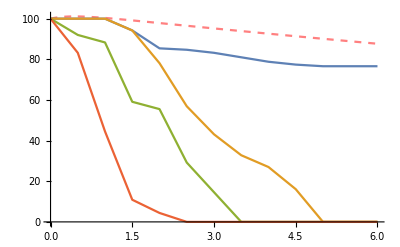

```mathematica
Show[Plot[fit0,{x,0,6}, PlotRange->{Min[dataA0,dataA5,dataA10,dataA15,fit0/.x-> Range[0,6,0.5]],Max[dataA0,dataA5,dataA10,dataA15,fit0/.x-> Range[0,6,0.5]]}, PlotStyle->{Pink,Dashed}],ListLinePlot[{dataA0,dataA5,dataA10,dataA15},DataRange->{0,6}]]
```

```mathematica
fit0/.x-> Range[0,6,0.5]
```

{100.,101.091,100.354,99.1501,97.8398,96.5154,95.201,93.9024,92.6209,91.3568,90.11,88.8801,87.667}

```mathematica
data = Join[{Range[0,6,0.5], ConstantArray[0,13], dataA0}ᵀ,{Range[0,6,0.5], ConstantArray[5,13], dataA5}ᵀ, {Range[0,6,0.5], ConstantArray[10,13], dataA10}ᵀ,{Range[0,6,0.5], ConstantArray[15,13], dataA15}ᵀ]
```

{{0.,0,100},{0.5,0,100},{1.,0,100},{1.5,0,94.2},{2.,0,85.4},{2.5,0,84.7},{3.,0,83.2},{3.5,0,81.},{4.,0,78.8},{4.5,0,77.4},{5.,0,76.6},{5.5,0,76.6},{6.,0,76.6},{0.,5,100},{0.5,5,100},{1.,5,100},{1.5,5,94.2},{2.,5,78.1},{2.5,5,56.9},{3.,5,43.1},{3.5,5,32.8},{4.,5,27},{4.5,5,16.1},{5.,5,0},{5.5,5,0},{6.,5,0},{0.,10,100},{0.5,10,92.},{1.,10,88.3},{1.5,10,59.1},{2.,10,55.5},{2.5,10,29.2},{3.,10,14.6},{3.5,10,0},{4.,10,0},{4.5,10,0},{5.,10,0},{5.5,10,0},{6.,10,0},{0.,15,100},{0.5,15,83.2},{1.,15,44.5},{1.5,15,10.9},{2.,15,4.4},{2.5,15,0},{3.,15,0},{3.5,15,0},{4.,15,0},{4.5,15,0},{5.,15,0},{5.5,15,0},{6.,15,0}}

```mathematica
dataNorm = (dataᵀ/{1,1,100})ᵀ
```

{{0.,0,1},{0.5,0,1},{1.,0,1},{1.5,0,0.942},{2.,0,0.854},{2.5,0,0.847},{3.,0,0.832},{3.5,0,0.81},{4.,0,0.788},{4.5,0,0.774},{5.,0,0.766},{5.5,0,0.766},{6.,0,0.766},{0.,5,1},{0.5,5,1},{1.,5,1},{1.5,5,0.942},{2.,5,0.781},{2.5,5,0.569},{3.,5,0.431},{3.5,5,0.328},{4.,5,27/100},{4.5,5,0.161},{5.,5,0},{5.5,5,0},{6.,5,0},{0.,10,1},{0.5,10,0.92},{1.,10,0.883},{1.5,10,0.591},{2.,10,0.555},{2.5,10,0.292},{3.,10,0.146},{3.5,10,0},{4.,10,0},{4.5,10,0},{5.,10,0},{5.5,10,0},{6.,10,0},{0.,15,1},{0.5,15,0.832},{1.,15,0.445},{1.5,15,0.109},{2.,15,0.044},{2.5,15,0},{3.,15,0},{3.5,15,0},{4.,15,0},{4.5,15,0},{5.,15,0},{5.5,15,0},{6.,15,0}}

```mathematica
FindFit[data, 100 Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{t , γ,β},{x,μ}, Method->NMinimize]
function =  100 Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
```

{t→0.0550243,γ→0.0472771,β→0.346716}

100 ⅇ^(-0.0472771 x+0.457727 (1-ⅇ^(-0.346716 x)-0.346716 x) μ)

```mathematica
Show[ ListPointPlot3D[data],Plot3D[function,{x,0,6},{μ, 0,15}, AxesLabel->Automatic]]
```

-Graphics3D-

```mathematica
FindFit[dataNorm, Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)],{μ, γ,β},{x,t}]
functionNorm =  Exp[-γ x + (t μ)/β^2(1-ⅇ^(-β x)-β x)]/. %
Show[ ListPointPlot3D[dataNorm],Plot3D[functionNorm,{x,0,6},{t, 0,15}, AxesLabel->Automatic,ColorFunction->(ColorData["SiennaTones"][#3]&)]]
```

{μ→0.0550244,γ→0.0472771,β→0.346718}

ⅇ^(0.457723 t (1-ⅇ^(-0.346718 x)-0.346718 x)-0.0472771 x)

-Graphics3D-